### 旧

```mathematica
WolframAlpha["www.douyin.com daily visitors history"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
da=WolframAlpha["www.douyin.com daily visitors history",{{"History:AlexaSiteVisitors:InternetData",1},"TimeSeriesData"}];
Export["PV.csv",Table[{DateString[DateObject[da⟦i,1⟧],{"Year",".","Month",".","Day"}],IntegerPart@QuantityMagnitude@N[da⟦i,2⟧]},{i,1,Length@da,1}]]
"PV.csv"
```

PV.csv

PV.csv

```mathematica
Export["date.csv",Table[{DateString[DateObject[da⟦i,1⟧],{"Year","年","Month","月","Day","日（星期","ISOWeekDay","）"}],IntegerPart@QuantityMagnitude@N[da⟦i,2⟧]},{i,1,Length@da,1}],CharacterEncoding-> "CP936"]
```

date.csv

### 下载 Alexa 数据

```mathematica
getPV[url_]:=WolframAlpha[url<>" daily visitors history",{{"History:AlexaSiteVisitors:InternetData",1},"TimeSeriesData"}];
```

```mathematica
urlLi={"douyu.com","panda.tv","huya.com","zhanqi.tv","longzhu.com","huomao.com","huajiao.com","yizhibo.com","quanmin.tv","chushou.tv"};
```

```mathematica
da=ConstantArray[0,{Length@urlLi,366,2}];
```

```mathematica
Table[
da⟦i⟧=getPV[urlLi⟦i⟧],
{i,1,Length@urlLi}];
```

```mathematica
(* 检查数据是否获取成功 *)
```

```mathematica
Table[{i,da⟦i,1⟧},{i,1,Length@da}]
```

```mathematica
(* 不成功的再多试几次就好了 *)
```

```mathematica
i=10;da⟦i⟧=getPV[urlLi⟦i⟧]
```

```mathematica
Save["D://saveda.wl",da]
```

```mathematica
(* 检查起止日期 *)
```

```mathematica
Table[{i,da⟦i,1,1⟧,IntegerPart@QuantityMagnitude@N[da⟦i,1,2⟧]},{i,1,Length@da}]
```

{{1,{2017,8,20,0,0,0.},9299708},{2,{2017,8,20,0,0,0.},1512480},{3,{2017,8,19,0,0,0.},258041},{4,{2017,8,20,0,0,0.},2728595},{5,{2017,8,20,0,0,0.},308116},{6,{2017,8,20,0,0,0.},659155},{7,{2017,8,19,0,0,0.},267239},{8,{2017,8,19,0,0,0.},164533},{9,{2017,8,19,0,0,0.},211542},{10,{2017,8,19,0,0,0.},173730}}

```mathematica
Table[{i,da⟦i,-1,1⟧,IntegerPart@QuantityMagnitude@N[da⟦i,-1,2⟧]},{i,1,Length@da}]
```

{{1,{2018,8,18,0,0,0.},7971178},{2,{2018,8,18,0,0,0.},16146746},{3,{2018,8,18,0,0,0.},2125647},{4,{2018,8,18,0,0,0.},11956767},{5,{2018,8,18,0,0,0.},381185},{6,{2018,8,18,0,0,0.},837995},{7,{2018,8,18,0,0,0.},153291},{8,{2018,8,18,0,0,0.},171687},{9,{2018,8,18,0,0,0.},628496},{10,{2018,8,18,0,0,0.},231982}}

### 再次处理数据

```mathematica
Get["D:\\D\\音视频\\可视化 TODO\\【折线加柱】视频网站访问量\\saveda.wl"];
da0=da;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["saveda.wl"];
```

```mathematica
daF=ConstantArray[0,{364,Length@urlLi+1}];
```

```mathematica
daF⟦All,1⟧=Table[DateObject[da0⟦1,i,1⟧],{i,1,Length[da0⟦1⟧],1}];
```

```mathematica
daF⟦All,2⟧=Table[IntegerPart@QuantityMagnitude@N[da⟦1,i,2⟧],{i,1,Length[da⟦1⟧],1}];
```

```mathematica
For[i=2,i≤Length@urlLi,i++,

j=2;p=1;
While[p≤Length[daF],

If[da⟦i,j,1⟧==da0⟦1,p,1⟧,
daF⟦p,i+1⟧=IntegerPart@QuantityMagnitude@N[da⟦i,j,2⟧];j++,
daF⟦p,i+1⟧=daF⟦j-1,i+1⟧
];
p++
(*Print[{p,j}]*)
];

Print[i]
]
```

2

3

4

5

6

7

8

9

10

```mathematica
Export["daF-bu.csv",daF]
```

daF-bu.csv

### debug 发现是有的开始日期超早

```mathematica
i=7;

j=2;p=1;
While[p≤Length[daF],

If[da⟦i,j,1⟧==da⟦1,p,1⟧,
daF⟦p,i+1⟧=IntegerPart@QuantityMagnitude@N[da⟦i,j,2⟧];j++,
daF⟦p,i+1⟧=daF⟦j-1,i+1⟧
];
p++
(*Print[{p,j}]*)
]

daF⟦All,i+1⟧
```

### 折线图

```mathematica
rd=Import["daF.csv",CharacterEncoding-> "CP936"];
```

```mathematica
rd[[2]]
```

{,斗鱼,熊猫TV,虎牙,战旗TV,龙珠,火猫,花椒,一直播,全民TV,触手TV}

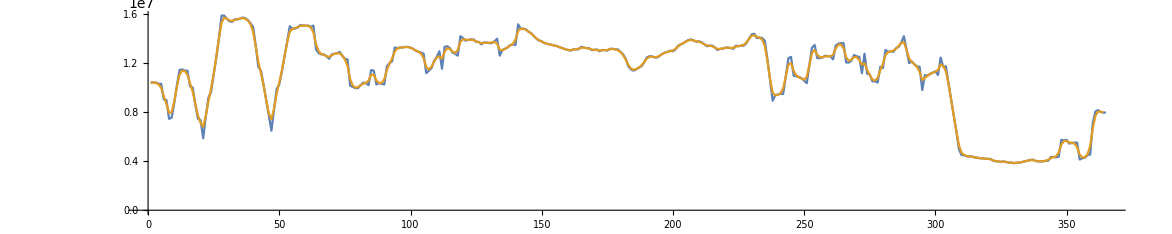

```mathematica
ListPlot[{rd⟦3;;367,2⟧,GaussianFilter[rd⟦3;;366,2⟧,2]},Joined->True,AspectRatio->1/5]
```

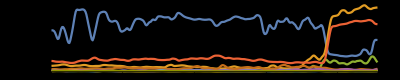

```mathematica
ListPlot[Table[GaussianFilter[rd⟦3;;367,i⟧,2],{i,2,11}],Joined->True,AspectRatio->1/5,PlotRange->All,Background->Black,PlotLegends->rd⟦2,2;;-1⟧]
```

```mathematica
Table[
rd⟦3;;-1,i⟧=IntegerPart@GaussianFilter[rd⟦3;;-1,i⟧,2]
,{i,2,9}];
```

```mathematica
Export["daF-gau.csv",rd,CharacterEncoding-> "CP936"];
```